```mathematica
SetDirectory[NotebookDirectory[]];
V=Flatten[Import["./VTOTAL.DAT"]];
T=Flatten[Import["./TMEV.DAT"]];
p=(V[[1]]-V)/T^4;
```

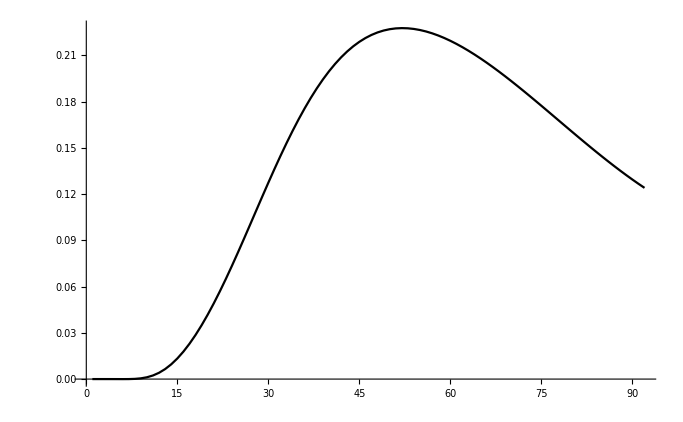

```mathematica
ListLinePlot[{p},PlotStyle->{Black,Dashed,Blue}]
```